```mathematica
ClearAll["Global`*"]
```

Load up packages

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
Needs["ComputerArithmetic`"]
```

```mathematica
dir="/SPENCEdata/Research/Satellites/FAST/kappa_dists/journals/";
SetDirectory[dir];
<<Liemohn_and_Khazanov__mapped_Maxwellian_density.wl
<<jvFuncs.wl
```

```mathematica
Get["funcs_for_stepMonitor_stringConv_plotSetOfInds_etc.m"]
(*Includes (as of 2018/03/29)
makeErrorData[x_,y_,yErr_]
kPlotStepMonitorData[kStepVals_]
gPlotStepMonitorData[gStepVals_]
tStringToSec[tString_]
minTidInd[tSearchString_,tStringArr_]
tPlotInds[inds_,mom_,momErr_,pRange_,xTitle_,yTitle_]
tPlotRange[ind1_,ind2_,mom_,momErr_,pRange_,xTitle_,yTitle_]
tablePlotMov[indStart_,indEnd1_,indEnd2_,mom_,momErr_,pRange_]
tablePlotsCombineAndAnimate[mov1_,mov2_]*)
```

## Define bounds of uniform distributions using 90% CIs for κ and and T dist fits

```mathematica
kappamin=1.8;
kappamax=3.3;
Tmin = 40;
Tmax=280;
nmin=0.05;
nmax=2.;
RBmin=8;
RBmax=200;
```

```mathematica
orbit=1612;
orbPref=ToString@StringForm["Orb`1`",orbit];
```

#### pot offset (in V)?

```mathematica
potTFactor=0;
```

## Example

```mathematica
(*Specify the seed?*)
```

```mathematica
(*seed=30;*)
```

```mathematica
(*SeedRandom[seed];*)
```

## Now give it a shot

#### Raw dater

```mathematica
(*1997-02-01/*)
```

```mathematica
time={"09:26:10.068","09:26:10.700","09:26:11.332","09:26:11.964","09:26:12.596","09:26:13.228",
"09:26:13.860","09:26:14.492","09:26:15.124","09:26:15.756","09:26:16.388","09:26:17.020","09:26:17.652",
"09:26:18.284","09:26:18.916","09:26:19.548","09:26:20.180","09:26:20.812","09:26:21.444","09:26:22.076",
"09:26:22.708","09:26:23.340","09:26:23.972","09:26:24.604","09:26:25.236","09:26:25.868","09:26:26.500",
"09:26:27.132","09:26:27.764","09:26:28.396","09:26:29.028","09:26:29.660","09:26:30.292","09:26:30.924",
"09:26:31.556","09:26:32.188","09:26:32.820","09:26:33.452","09:26:34.084","09:26:34.716","09:26:35.348",
"09:26:35.980","09:26:36.612","09:26:37.244","09:26:37.876","09:26:38.508","09:26:39.140","09:26:39.773",
"09:26:40.405","09:26:41.037","09:26:41.669","09:26:42.301","09:26:42.933","09:26:43.565","09:26:44.197",
"09:26:44.829","09:26:45.461","09:26:46.093","09:26:46.725","09:26:47.357","09:26:47.989","09:26:48.621",
"09:26:49.253","09:26:49.885","09:26:50.517","09:26:51.149","09:26:51.781","09:26:52.413","09:26:53.045",
"09:26:53.677","09:26:54.309","09:26:54.941","09:26:55.573","09:26:56.205","09:26:56.837","09:26:57.469",
"09:26:58.101","09:26:58.733","09:26:59.365","09:26:59.997","09:27:00.629","09:27:01.261","09:27:01.893",
"09:27:02.525","09:27:03.157","09:27:03.789","09:27:04.422","09:27:05.054","09:27:05.686","09:27:06.318",
"09:27:06.950","09:27:07.582","09:27:08.214","09:27:08.846","09:27:09.478","09:27:10.110","09:27:10.742",
"09:27:11.374","09:27:12.006","09:27:12.638","09:27:13.270","09:27:13.902","09:27:14.534"};
pots={344.960,564.480,815.360,1128.960,1790.880,1823.360,2119.040,3153.920,3297.280,3109.120,2903.040,2222.080,1680.000,1868.160,18244.160,4587.520,4193.280,4838.400,5429.760,4838.400,
5214.720,4838.400,5214.720,5537.280,5214.720,5214.720,5967.360,7383.041,6809.599,5806.080,6809.599,7598.080,6307.840,6594.560,6594.560,6218.240,7096.320,5797.120,6406.400,5519.360,
5402.880,8099.840,7598.080,8099.840,8099.840,7687.680,6720.000,5824.000,4032.000,3360.000,2714.880,2464.000,1769.600,2024.960,1827.840,1827.840,2213.120,2464.000,2213.120,2213.120,
2222.080,2419.200,2096.640,2024.960,2024.960,2024.960,1827.840,1899.520,1232.000,1303.680,788.480,1232.000,1146.880,1209.600,616.000,470.400,344.960,344.960,985.600,344.960,344.960,
344.960,344.960,344.960}; 
curs={0.072,0.449,1.094,1.482,2.091,1.795,1.710,1.875,1.712,1.613,1.844,1.750,1.773,1.706,1.819,1.694,1.725,1.494,1.985,1.637,1.775,2.032,2.388,2.322,2.089,1.620,1.707,1.178,1.556,
1.875,2.162,2.194,2.392,1.717,1.831,1.890,1.877,1.758,1.799,1.838,2.136,2.521,2.214,1.901,1.968,1.435,1.424,2.087,2.168,1.996,2.001,2.165,1.780,1.883,1.548,2.576,3.412,4.258,5.238,
4.815,4.018,2.553,2.447,3.542,3.515,3.820,3.385,2.487,2.367,1.782,1.780,1.628,1.636,1.749,1.708,2.143,2.591,2.683,2.548,2.271,2.462,2.208,2.468,2.240,2.011,2.060,1.718,1.499,
1.391,1.463,1.681,0.646,0.592,0.251,0.187,0.240,0.813,0.156,0.165,0.134,0.220,0.217,0.219}; 
curErrs={0.013,0.037,0.050,0.056,0.073,0.059,1.701,0.103,0.052,0.057,0.067,0.062,0.068,0.057,0.071,0.066,0.059,0.064,0.078,0.064,0.351,0.081,0.092,0.092,0.087,0.073,0.077,0.057,
0.097,0.242,0.077,0.111,0.097,0.082,0.089,0.086,0.103,0.093,0.097,0.083,0.104,0.136,0.131,0.104,0.124,0.074,0.387,0.108,0.096,0.146,0.093,0.221,0.142,0.135,0.113,0.153,0.165,0.270,
0.225,0.301,0.305,0.182,0.152,0.191,0.248,0.274,0.218,0.199,0.156,0.153,0.209,0.146,0.123,0.281,0.206,0.195,0.086,0.073,0.078,0.082,0.068,0.069,0.071,0.065,0.197,0.130,0.143,0.111,
0.103,0.225,0.061,0.095,0.044,0.035,0.024,0.023,0.052,0.021,0.026,0.023,0.026,0.022,0.024};
je={0.064,0.367,1.134,1.910,3.324,2.232,2.020,1.738,1.443,1.231,1.688,1.461,1.703,1.579,1.736,1.441,1.448,1.217,2.166,1.643,1.915,3.034,3.910,3.967,3.092,1.852,1.950,0.957,1.996,
3.217,4.604,4.261,4.301,3.026,2.840,3.244,3.219,2.992,3.365,3.188,4.611,6.197,6.222,4.098,4.336,2.388,3.042,5.892,5.950,5.978,5.450,5.726,4.013,4.280,3.364,7.328,14.440,18.881,
23.148,22.930,16.671,9.344,8.979,16.256,14.969,14.080,10.706,4.892,4.169,2.455,2.032,1.684,1.480,1.518,1.546,2.184,2.864,2.880,2.556,2.039,2.221,1.837,2.203,1.907,1.872,1.922,1.416,
1.039,0.878,0.805,0.968,0.411,0.360,0.164,0.126,0.135,0.716,0.111,0.109,0.075,0.133,0.119,0.128}; 
jeErr={0.109,0.229,0.167,NaN,0.402,0.311,2.649,0.272,0.268,0.340,0.348,0.264,0.334,0.269,0.334,0.294,0.412,0.264,0.356,0.302,1.394,0.563,7.206,0.503,0.482,0.345,0.344,0.650,
0.501,0.636,0.547,0.762,0.955,0.569,0.537,0.610,7.148,0.809,0.670,0.612,0.868,1.733,1.024,0.787,1.537,0.498,1.085,0.989,0.982,2.187,1.009,1.933,1.464,1.175,4.092,1.582,2.062,
2.323,1.628,2.504,3.844,2.214,1.724,2.271,3.485,2.954,2.408,4.737,2.148,0.672,1.137,1.428,0.800,1.320,0.823,1.196,0.440,0.466,0.309,0.294,0.310,0.300,0.313,0.279,2.555,0.608,
0.792,0.298,0.260,0.282,0.216,0.693,0.115,0.095,0.067,0.045,0.114,0.043,0.180,0.056,0.096,0.106,0.188};
```

```mathematica
itvl1Tids={"09:26:11.332","09:26:22.708"};
itvl2Tids={"09:26:56.837","09:27:06.950"};
```

```mathematica
(*itvl1Bounds={Flatten@((minTidInd[#,time])&/@upIonTidM1),Flatten@((minTidInd[#,time])&/@upIonTidM2)};*)
```

```mathematica
(*itvl1Inds=Flatten@MapThread[Range,Transpose@itvl1Bounds];*)
```

```mathematica
itvl1Bounds=Flatten@((minTidInd[#,time])&/@itvl1Tids);
```

```mathematica
itvl1Inds=Range@@itvl1Bounds;
```

```mathematica
itvl2Bounds=Flatten@((minTidInd[#,time])&/@itvl2Tids);
```

```mathematica
itvl2Inds=Range@@itvl2Bounds;
```

#### Select interval

```mathematica
interval=1;
```

```mathematica
interval=2;
```

```mathematica
Print[ToString@StringForm["Using interval `1` ...",interval]]
```

Using interval 1 ...

#### Init data

```mathematica
{plotData1}=(Partition[Riffle[pots[[#]]+potTFactor,curs[[#]]],2])&/@{inds1};
```

```mathematica
errorPot1=potErrs[[inds1]];
```

```mathematica
{errorData1}=(makeErrorData[pots[[#]]+potTFactor,curs[[#]],curErrs[[#]]])&/@{inds1};
```

```mathematica
Switch[interval,
1,
inds=itvl1Inds;,
2,
inds=itvl2Inds;]
tid=time[[inds]];
jData=(Partition[Riffle[pots[[#]]+potTFactor,curs[[#]]],2])&/@{inds};
jErrData=(makeErrorData[pots[[#]]+potTFactor,curs[[#]],curErrs[[#]]])&/@{inds};
jWt=(1/(curErrs[[#]])^2)&/@{inds};
potErr
potVal=jData[[;;,1]];
nPots=Length@potVal;
```

```mathematica
curVal=jData[[;;,2]];
```

```mathematica
potErr={159.53,159.53,116.82,116.82,116.82,79.76,79.76,79.76,79.76,79.76,116.82,116.82,116.82,134.77,79.76,67.39,67.39,63.92};
curErr={0.057,0.046,0.035,0.035,0.041,0.047,0.041,0.049,0.04,0.039,0.039,0.043,0.041,0.047,0.048,0.043,0.045,0.05};,
```

#### Which fit method to use?

```mathematica
(*fitMethod="LevenbergMarquardt";*)
```

```mathematica
(*fitMethod="ConjugateGradient";*)
(*fitMethod="Gradient";*)
(*fitMethod="Newton";*)
```

```mathematica
fitMethod={"NMinimize",Method->"NelderMead"};
```

```mathematica
fitMethod={"NMinimize",Method->"DifferentialEvolution"};
```

```mathematica
fitMethod={"NMinimize",Method->"SimulatedAnnealing"};
```

```mathematica
fitMethod={"NMinimize",Method->"RandomSearch"};
```

```mathematica
fitMethod=Automatic;
```

```mathematica
If[Length@fitMethod==2,fitMethodString=ToString@StringForm["`1`__`2`",fitMethod[[1]],ToString@Values@fitMethod[[2]]],fitMethodString=fitMethod];
```

#### Bounds

```mathematica
minFitT=115;
maxFitT=125;
minFitRB=2;
maxFitRB=100;
minFitN=0.1;
maxFitN=2;
minFitKappa=Switch[interval,
1,3.84,
2,2.24];
maxFitKappa=35;
```

#### Init model setter uppers

Now Kappa

```mathematica
Options[kFitVarSetup]={fixT->False,fixN->False,fixRB-> False,fixKappa-> False};
kFitVarSetup[OptionsPattern[]]:=Module[{fitVars},
fitVars={};
If[OptionValue[fixN]==False,fitVars=Append[fitVars,{kFitN,kFitNinit}]];
If[OptionValue[fixT]==False,fitVars=Append[fitVars,{kFitT,kFitTinit}]];
If[OptionValue[fixRB]==False,fitVars=Append[fitVars,{kFitRB,kFitRBinit}]];
If[OptionValue[fixKappa]==False,fitVars=Append[fitVars,{kFitKappa,kFitKappainit}]];
fitVars
]
```

```mathematica
Options[kConstraintSetup]={fixT->False,fixN->False,fixRB-> False,fixKappa-> False};
kConstraintSetup[OptionsPattern[]]:=Module[{constraints},
constraints={};
If[OptionValue[fixN]==False,constraints=Append[constraints,minFitN<kFitN<maxFitN]];
If[OptionValue[fixT]==False,constraints=Append[constraints,minFitT<kFitT<maxFitT]];
If[OptionValue[fixRB]==False,constraints=Append[constraints,minFitRB<kFitRB<maxFitRB]];
If[OptionValue[fixKappa]==False,constraints=Append[constraints,minFitKappa<kFitKappa<maxFitKappa]];
constraints
]
```

```mathematica
Options[kFitModelSetup]={fixT->False,fixN->False,fixRB-> False,fixKappa-> False};
kFitModelSetup[OptionsPattern[]]:=Module[{fitModel},
fitModel=JVKappa[pot,kFitRB,kFitT,kFitN,kFitKappa];
If[NumberQ@OptionValue[fixN],fitModel=fitModel/.{kFitN->OptionValue[fixN]}];
If[NumberQ@OptionValue[fixT],fitModel=fitModel/.{kFitT->OptionValue[fixT]}];
If[NumberQ@OptionValue[fixRB],fitModel=fitModel/.{kFitRB->OptionValue[fixRB]}];
If[NumberQ@OptionValue[fixKappa],fitModel=fitModel/.{kFitKappa->OptionValue[fixKappa]}];
fitModel
]
```

```mathematica
Options[kFitOutputSetup]={fixT->False,fixN->False,fixRB-> False,fixKappa-> False};
kFitOutputSetup[OptionsPattern[]]:=Module[{fitOutput},
fitOutput={kFitN,kFitT,kFitRB,kFitKappa,kFitChi2red};
If[NumberQ@OptionValue[fixN],fitOutput=fitOutput/.{kFitN->OptionValue[fixN]}];
If[NumberQ@OptionValue[fixT],fitOutput=fitOutput/.{kFitT->OptionValue[fixT]}];
If[NumberQ@OptionValue[fixRB],fitOutput=fitOutput/.{kFitRB->OptionValue[fixRB]}];
If[NumberQ@OptionValue[fixKappa],fitOutput=fitOutput/.{kFitKappa->OptionValue[fixKappa]}];
fitOutput
]
```

```mathematica
Options[kFitValAddsSetup]={fixT->False,fixN->False,fixRB-> False,fixKappa-> False};
kFitValAddsSetup[OptionsPattern[]]:=Module[{fitValAdds},
fitValAdds={};
If[NumberQ@OptionValue[fixN],fitValAdds=Append[fitValAdds,kFitN->OptionValue[fixN]];];
If[NumberQ@OptionValue[fixT],fitValAdds=Append[fitValAdds,kFitT->OptionValue[fixT]];];
If[NumberQ@OptionValue[fixRB],fitValAdds=Append[fitValAdds,kFitRB->OptionValue[fixRB]];];
If[NumberQ@OptionValue[fixKappa],fitValAdds=Append[fitValAdds,kFitKappa->OptionValue[fixKappa]];];
fitValAdds
]
```

```mathematica
Options[kDOFSetup]={fixT->False,fixN->False,fixRB-> False,fixKappa-> False};
kDOFSetup[OptionsPattern[]]:=Module[{count},
count=4;
If[NumberQ@OptionValue[fixN],count--];
If[NumberQ@OptionValue[fixT],count--];
If[NumberQ@OptionValue[fixRB],count--];
If[NumberQ@OptionValue[fixKappa],count--];
count
]
```

```mathematica
Options[kFixStringSetup]={fixT->False,fixN->False,fixRB-> False,fixKappa-> False};
kFixStringSetup[OptionsPattern[]]:=Module[{fixString},
fixString="";
If[NumberQ@OptionValue[fixN],fixString=fixString<>(StringReplace[ToString@StringForm["-fixN`1`",OptionValue[fixN]],"."->"_"])];
If[NumberQ@OptionValue[fixT],fixString=fixString<>(StringReplace[ToString@StringForm["-fixT`1`eV",OptionValue[fixT]],"."->"_"])];
If[NumberQ@OptionValue[fixRB],fixString=fixString<>(StringReplace[ToString@StringForm["-fixRB`1`",OptionValue[fixRB]],"."->"_"])];
If[NumberQ@OptionValue[fixKappa],fixString=fixString<>(StringReplace[ToString@StringForm["-fixKappa`1`",OptionValue[fixKappa]],"."->"_"])];
fixString
]
```

```mathematica
Options[gFixStringSetup]={fixT->False,fixN->False,fixRB-> False};
gFixStringSetup[OptionsPattern[]]:=Module[{fixString},
fixString="";
If[NumberQ@OptionValue[fixN],fixString=fixString<>(StringReplace[ToString@StringForm["-fixN`1`",OptionValue[fixN]],"."->"_"])];
If[NumberQ@OptionValue[fixT],fixString=fixString<>(StringReplace[ToString@StringForm["-fixT`1`eV",OptionValue[fixT]],"."->"_"])];
If[NumberQ@OptionValue[fixRB],fixString=fixString<>(StringReplace[ToString@StringForm["-fixRB`1`",OptionValue[fixRB]],"."->"_"])];
fixString
]
```

Now Maxwellian setup

```mathematica
Options[gFitVarSetup]={fixT->False,fixN->False,fixRB-> False};
gFitVarSetup[OptionsPattern[]]:=Module[{fitVars},
fitVars={};
If[OptionValue[fixN]==False,fitVars=Append[fitVars,{gFitN,gFitNinit}]];
If[OptionValue[fixT]==False,fitVars=Append[fitVars,{gFitT,gFitTinit}]];
If[OptionValue[fixRB]==False,fitVars=Append[fitVars,{gFitRB,gFitRBinit}]];
fitVars
]
```

```mathematica
Options[gConstraintSetup]={fixT->False,fixN->False,fixRB-> False};
gConstraintSetup[OptionsPattern[]]:=Module[{constraints},
constraints={};
If[OptionValue[fixN]==False,constraints=Append[constraints,minFitN<gFitN<maxFitN]];
If[OptionValue[fixT]==False,constraints=Append[constraints,minFitT<gFitT<maxFitT]];
If[OptionValue[fixRB]==False,constraints=Append[constraints,minFitRB<gFitRB<maxFitRB]];
constraints
]
```

```mathematica
Options[gFitModelSetup]={fixT->False,fixN->False,fixRB-> False};
gFitModelSetup[OptionsPattern[]]:=Module[{fitModel},
fitModel=JVMaxwellian[pot,gFitRB,gFitT,gFitN];
If[NumberQ@OptionValue[fixN],fitModel=fitModel/.{gFitN->OptionValue[fixN]}];
If[NumberQ@OptionValue[fixT],fitModel=fitModel/.{gFitT->OptionValue[fixT]}];
If[NumberQ@OptionValue[fixRB],fitModel=fitModel/.{gFitRB->OptionValue[fixRB]}];
fitModel
]
```

```mathematica
Options[gFitOutputSetup]={fixT->False,fixN->False,fixRB-> False};
gFitOutputSetup[OptionsPattern[]]:=Module[{fitOutput},
fitOutput={gFitN,gFitT,gFitRB,gFitKappa,gFitChi2red};
If[NumberQ@OptionValue[fixN],fitOutput=fitOutput/.{gFitN->OptionValue[fixN]}];
If[NumberQ@OptionValue[fixT],fitOutput=fitOutput/.{gFitT->OptionValue[fixT]}];
If[NumberQ@OptionValue[fixRB],fitOutput=fitOutput/.{gFitRB->OptionValue[fixRB]}];
fitOutput
]
```

```mathematica
Options[gFitValAddsSetup]={fixT->False,fixN->False,fixRB-> False};
gFitValAddsSetup[OptionsPattern[]]:=Module[{fitValAdds},
fitValAdds={};
If[NumberQ@OptionValue[fixN],fitValAdds=Append[fitValAdds,gFitN->OptionValue[fixN]];];
If[NumberQ@OptionValue[fixT],fitValAdds=Append[fitValAdds,gFitT->OptionValue[fixT]];];
If[NumberQ@OptionValue[fixRB],fitValAdds=Append[fitValAdds,gFitRB->OptionValue[fixRB]];];
fitValAdds
]
```

```mathematica
Options[gDOFSetup]={fixT->False,fixN->False,fixRB-> False};
gDOFSetup[OptionsPattern[]]:=Module[{count},
count=3;
If[NumberQ@OptionValue[fixN],count--];
If[NumberQ@OptionValue[fixT],count--];
If[NumberQ@OptionValue[fixRB],count--];
count
]
```

```mathematica
Options[genMCStartupMessage]={fixT->False,fixN->False,fixRB-> False,fixKappa-> False};
genMCStartupMessage[OptionsPattern[]]:=Module[{count},
Print[ToString@StringForm["Interval: `1`",interval]];
If[NumberQ@OptionValue[fixN],Print[ToString@StringForm["fixN    : `1`",OptionValue[fixN]]]];
If[NumberQ@OptionValue[fixT],Print[ToString@StringForm["fixT    : `1`",OptionValue[fixT]]]];
If[NumberQ@OptionValue[fixRB],Print[ToString@StringForm["fixRB   : `1`",OptionValue[fixRB]]]];
If[NumberQ@OptionValue[fixKappa],Print[ToString@StringForm["fixKappa: `1`",OptionValue[fixKappa]]]];
]
```

#### Now fixies

```mathematica
doFixT=True;
```

```mathematica
(*kfixTVal:=Switch[doFixT,True,Switch[interval,1,140,2,180],False,False];
gfixTVal:=Switch[doFixT,True,Switch[interval,1,120,2,140],False,False];*)
kfixTVal:=Switch[doFixT,True,Switch[interval,1,124,2,193],False,False];
gfixTVal:=Switch[doFixT,True,Switch[interval,1,140,2,117],False,False];
kfixNVal=False;
gfixNVal=False;
kfixRBVal= False;
gfixRBVal= False;
fixKappaVal= Switch[interval,1,5.4,2,2.6];
```

#### Init models

```mathematica
kModel=kFitModelSetup[fixT->kfixTVal,fixN->kfixNVal,fixRB->kfixRBVal,fixKappa->fixKappaVal];
gModel=gFitModelSetup[fixT->gfixTVal,fixN->gfixNVal,fixRB->gfixRBVal];
```

```mathematica
kFitVars:=kFitVarSetup[fixT->kfixTVal,fixN->kfixNVal,fixRB->kfixRBVal,fixKappa->fixKappaVal];
gFitVars:=gFitVarSetup[fixT->gfixTVal,fixN->gfixNVal,fixRB->gfixRBVal];
```

```mathematica
kConstraints=kConstraintSetup[fixT->kfixTVal,fixN->kfixNVal,fixRB->kfixRBVal,fixKappa->fixKappaVal];
gConstraints=gConstraintSetup[fixT->gfixTVal,fixN->gfixNVal,fixRB->gfixRBVal];
```

```mathematica
kFitOutput:=kFitOutputSetup[fixT->kfixTVal,fixN->kfixNVal,fixRB->kfixRBVal,fixKappa->fixKappaVal];
gFitOutput:=gFitOutputSetup[fixT->gfixTVal,fixN->gfixNVal,fixRB->gfixRBVal];
```

```mathematica
kFitValAdds=kFitValAddsSetup[fixT->kfixTVal,fixN->kfixNVal,fixRB->kfixRBVal,fixKappa->fixKappaVal];
gFitValAdds=gFitValAddsSetup[fixT->gfixTVal,fixN->gfixNVal,fixRB->gfixRBVal];
```

```mathematica
kDOF=nPots-kDOFSetup[fixT->kfixTVal,fixN->kfixNVal,fixRB->kfixRBVal,fixKappa->fixKappaVal];
gDOF=nPots-gDOFSetup[fixT->gfixTVal,fixN->gfixNVal,fixRB->gfixRBVal];
```

```mathematica
kFixString:=kFixStringSetup[fixT->kfixTVal,fixN->kfixNVal,fixRB->kfixRBVal,fixKappa->fixKappaVal];
gFixString:=gFixStringSetup[fixT->gfixTVal,fixN->gfixNVal,fixRB->gfixRBVal];
```

```mathematica
kMCStartupMessage:=genMCStartupMessage[fixT->kfixTVal,fixN->kfixNVal,fixRB->kfixRBVal,fixKappa->fixKappaVal];
gMCStartupMessage:=genMCStartupMessage[fixT->gfixTVal,fixN->gfixNVal,fixRB->gfixRBVal];
```

Unconstrain if fitMethod requires it

```mathematica
If[Head@fitMethod==String,If[
fitMethod=="LevenbergMarquardt"||fitMethod=="ConjugateGradient",kConstraints=None;gConstraints=None;kCombConstraints=None;gCombConstraints=None;kDoubledConstraints=None;gDoubledConstraints=None;]];
```

#### Initial fit

```mathematica
kinitParams = RandomReal/@{{nmin,nmax},{Tmin,Tmax},{RBmin,RBmax},{kappamin,kappamax}};
{kFitNinit,kFitTinit,kFitRBinit,kFitKappainit}=kinitParams;
ginitParams = RandomReal/@{{nmin,nmax},{Tmin,Tmax},{RBmin,RBmax}};
{gFitNinit,gFitTinit,gFitRBinit}=ginitParams;
```

```mathematica
kInitialFit=NonlinearModelFit[jData,(If[Length@kConstraints≠0,{kModel,kConstraints},kModel]),kFitVars,pot,Weights->jWt,VarianceEstimatorFunction->(1&),Method->fitMethod];
gInitialFit=NonlinearModelFit[jData,{gModel,gConstraints},gFitVars,pot,Weights->jWt,VarianceEstimatorFunction->(1&),Method->fitMethod];
```

```mathematica
kInitialFitVals:=Append[Flatten@Append[kInitialFit["BestFitParameters"],kFitValAdds],kFitChi2red->Total[(kInitialFit["FitResiduals"])^2*jWt]/kDOF]
```

```mathematica
gInitialFitVals:=Append[Flatten@Append[gInitialFit["BestFitParameters"],gFitValAdds],gFitChi2red->Total[(gInitialFit["FitResiduals"])^2*jWt]/gDOF]
```

#### ‘Nitialize strings ‘n’ things

```mathematica
orbPref=ToString@StringForm["Orb`1`_",orbit];
```

```mathematica
plotDir="/SPENCEdata/Research/Satellites/FAST/kappa_dists/plots/"<>(ToString@DateString[{"Year","Month","Day","/"}]);
saveDir="/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/"<>(ToString@DateString[{"Year","Month","Day","/"}]);
```

```mathematica
If[!FileExistsQ[plotDir],CreateDirectory[plotDir];Print["Nå har du det!"]];
If[!FileExistsQ[saveDir],CreateDirectory[saveDir];Print["Nå har du det!"]]
```

Nå har du det!

```mathematica
kFString:=ToString@StringForm["itvl`1`_kappa`2`_nRolls`3`",interval,kFixString,nTrials];
gFString:=ToString@StringForm["itvl`1`_Maxwell`2`_nRolls`3`",interval,gFixString,nTrials];
```

```mathematica
datFSuff=".wdx";
plotExt=".pdf";
histosPlotSuff="__histograms"<>plotExt;
smoothHistosPlotSuff="__smoothHistograms"<>plotExt;
densityHistoSuff="__smoothDensityHistogram"<>plotExt;
```

```mathematica
(*{kDataFile,kHistosPlotFile,kDensityHistoFile}=(orbPref<>kFString<>#)&/@{datFSuff,histosPlotSuff,densityHistoSuff};*)
kDataFile:=(orbPref<>kFString<>#)&[datFSuff];
kHistosPlotFile:=(orbPref<>kFString<>#)&[histosPlotSuff];
kSmoothHistosPlotFile:=(orbPref<>gFString<>#)&[smoothHistosPlotSuff];
kDensityHistoFile:=(orbPref<>kFString<>#)&[densityHistoSuff];
initFitFile:=saveDir<>(ToString@StringForm["`1`_initialFits.wdx",kFString])
```

```mathematica
{gDataFile,gHistosPlotFile,gDensityHistoFile}=(orbPref<>gFString<>#)&/@{datFSuff,histosPlotSuff,densityHistoSuff};
gDataFile:=(orbPref<>gFString<>#)&[datFSuff];
gHistosPlotFile:=(orbPref<>gFString<>#)&[histosPlotSuff];
gSmoothHistosPlotFile:=(orbPref<>gFString<>#)&[smoothHistosPlotSuff];
gDensityHistoFile:=(orbPref<>gFString<>#)&[densityHistoSuff];
```

#### Setup plot ranges

```mathematica
minPot=Min[potVal ]* 8/10;maxPot=Max[potVal]*1.1;
```

```mathematica
minJ=Min[curVal]/1.8;maxJ=Max[curVal]*1.2;
```

#### Other plot stuff

```mathematica
parNames=Style[#,Bold]&/@{"T_m    : ","n_m    : ","R_B   : ","χ_red^2   :"};
pTableVSpace=0.5;
pTableFontSize=14;
pTableScaledLoc={0.12,0.65};
```

```mathematica
titleSize=20;
```

```mathematica
axesLabelSize=18;
```

```mathematica
gJVVals=(MapThread[NumberForm,{({gFitT,gFitN}/.gInitialFitVals),{{3,0},{3,2}}}])~Join~{ScientificForm[gFitRB,3]/.gInitialFitVals}~Join~{NumberForm[gFitChi2red,3]/.gInitialFitVals};
kJVVals=(MapThread[NumberForm,{({kFitT,kFitN}/.kInitialFitVals),{{3,0},{3,2}}}])~Join~{ScientificForm[kFitRB,3]/.kInitialFitVals}~Join~{NumberForm[kFitChi2red,3]/.kInitialFitVals};
```

```mathematica
JVParTable=Text[Grid[Transpose[{{Style["Maxwell",Bold,(ColorData[97,"ColorList"])[[1]]]}~Join~parNames~Join~{Style["Kappa  :",Bold,(ColorData[97,"ColorList"])[[2]]]}~Join~parNames,{""}~Join~gJVVals~Join~{(ToString@StringForm["`1`",NumberForm[kFitKappa/.kInitialFitVals,3]])}~Join~kJVVals}],Alignment->".",Spacings->{0,pTableVSpace},ItemStyle->Directive[FontSize->pTableFontSize]]];
```

```mathematica
initTitle=StringJoin@Riffle[tid[[{1,-1}]],"–"];
```

#### Ze plot

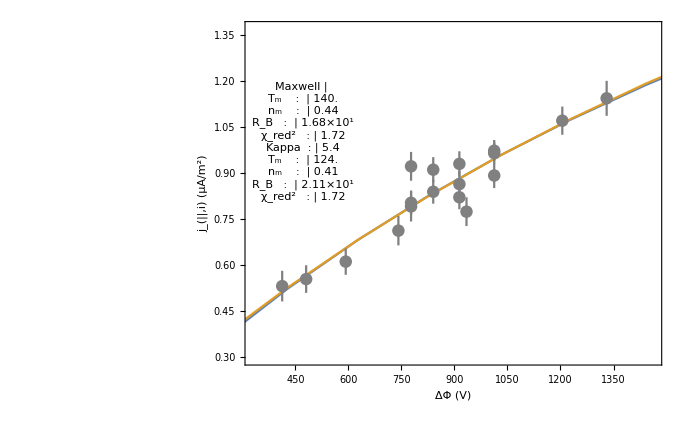

```mathematica
JVInitFitPlot=Show[Plot[{kInitialFit[pot],gInitialFit[pot]},{pot,20,10000},PlotRange->{{minPot,maxPot},{minJ,maxJ}},Frame->True,FrameLabel->{{"j_(||,i) (μA/m^2)",""},{"ΔΦ (V)",Style[StringForm["Interval `1` (`2`)",interval,initTitle],Bold,titleSize]}},ImageSize->700,FrameStyle->Directive[Black,axesLabelSize],Epilog->Inset[JVParTable,Scaled[{0.14,0.65}]]],ErrorListPlot[jErrData,PlotStyle->Gray]]
```

```mathematica
If[saveDataFiles,
DumpSave[initFitFile,{kInitialFit,gInitialFit,JVParTable,jErrData,initTitle,tid,jData,jErrData,jWt,potErr,curErr,potVal,curVal}];
Print["Saved "<>initFitFile];]
```

Saved /SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/20180413/itvl2_kappa-fixT193eV-fixKappa2_6_nRolls5000_initialFits.wdx

#### Some Monte Carlo stuff for generating current uncertainty and potential uncertainty

```mathematica
genMCError:=RandomVariate[NormalDistribution[],nPots]*curErr[[currentInds]]
```

```mathematica
genPotVals:=potVal[[currentInds]]+RandomReal[{0,1},nPots]*potErr[[currentInds]]
```

```mathematica
inds=Range[1,nPots];
```

#### Visualize, Plot, See what synthetic data look like

```mathematica
currentInds=RandomChoice[inds,nPots];
```

```mathematica
curMCError=genMCError;
curPotVals=genPotVals;
```

```mathematica
curError=curErr[[currentInds]];
```

```mathematica
curjData=Partition[Riffle[curPotVals,((kInitialFit[#])&/@curPotVals)+curMCError],2];
```

```mathematica
curErrData=makeErrorData[curPotVals,curjData[[;;,2]],curError];
```

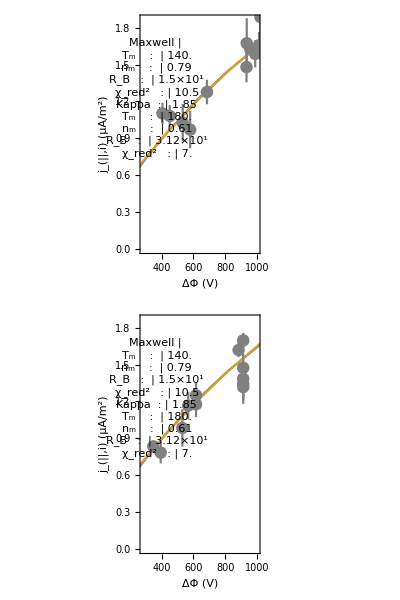

```mathematica
JVInitVsSynthPlot=Column[{Show[Plot[{kInitialFit[pot],gInitialFit[pot]},{pot,20,10000},PlotRange->{{minPot,maxPot},{minJ,maxJ}},Frame->True,FrameLabel->{{"j_(||,i) (μA/m^2)",""},{"ΔΦ (V)",Style[StringForm["J-V Fit (`1`)",initTitle],Bold,titleSize]}},ImageSize->700,FrameStyle->Directive[Black,axesLabelSize],Epilog->Inset[JVParTable,Scaled[{0.14,0.65}]]],ErrorListPlot[curErrData,PlotStyle->Gray]],Show[Plot[{kInitialFit[pot],gInitialFit[pot]},{pot,20,10000},PlotRange->{{minPot,maxPot},{minJ,maxJ}},Frame->True,FrameLabel->{{"j_(||,i) (μA/m^2)",""},{"ΔΦ (V)",Style[StringForm["J-V Fit (`1`)",initTitle],Bold,titleSize]}},ImageSize->700,FrameStyle->Directive[Black,axesLabelSize],Epilog->Inset[JVParTable,Scaled[{0.14,0.65}]]],ErrorListPlot[jErrData,PlotStyle->Gray]]}]
```

Do the Monte Carloing

```mathematica
countItvl=50;
currentInds=inds;
makePlots=True;
```

#### Some options

```mathematica
doBootstrap=False;
nTrials=5000;
saveDataFiles=True;
```

#### Kappa block

```mathematica
Block[{trials=nTrials, count=0,currentInds,curMCError,curPotVals,curjData,
kinitParams,kFitNinit,kFitTinit,kFitRBinit,kFitKappainit,kFit},
kMCStartupMessage;
kFitVals:=Flatten@Append[{Flatten@Append[{kFit["BestFitParameters"]},kFitValAdds]},kFitChi2red->Total[(kFit["FitResiduals"])^2*curWt]/kDOF];
If[doBootstrap==False,currentInds=inds;];
Monitor[kFits=Table[
(*If[Mod[count,countItvl]==0,Print[ToString@StringForm["Count: `1`",count]]];*)
If[doBootstrap,currentInds=RandomChoice[inds,nPots];];
curMCError=genMCError;
curError=curErr[[currentInds]];
curWt=1/curError^2;
curPotVals=genPotVals;
curjData=Partition[Riffle[curPotVals,((kInitialFit[#])&/@curPotVals)+curMCError],2];
kinitParams = RandomReal/@{{nmin,nmax},{Tmin,Tmax},{RBmin,RBmax},{kappamin,kappamax}};
{kFitNinit,kFitTinit,kFitRBinit,kFitKappainit}=kinitParams;
kFit=NonlinearModelFit[curjData,(If[Length@kConstraints≠0,{kModel,kConstraints},kModel]),kFitVars,pot,Weights->curWt,VarianceEstimatorFunction->(1&),Method->fitMethod];
count++;
(*{count, kFit["BestFitParameters"],kinitParams,kFit},trials];]*)
{count,Evaluate[ kFitOutput/.kFitVals],kinitParams,kFit},trials];,count]
];
```

Interval: 2

fixT    : 193

fixKappa: 2.6

```mathematica
If[saveDataFiles,DumpSave[(saveDir<>kDataFile),kFits];Print["Saved to "<>saveDir<>kDataFile]]
```

Saved to /SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/20180413/Orb1612_itvl2_kappa-fixT193eV-fixKappa2_6_nRolls5000.wdx

#### Maxwell block

```mathematica
Block[{trials=nTrials, count=0,currentInds,curMCError,curPotVals,curjData,
ginitParams,gFitNinit,gFitTinit,gFitRBinit,gFit},
gMCStartupMessage;
gFitVals:=Flatten@Append[{Flatten@Append[{gFit["BestFitParameters"]},gFitValAdds]},gFitChi2red->Total[(gFit["FitResiduals"])^2*curWt]/gDOF];
If[doBootstrap==False,currentInds=inds;];
gFits=Monitor[Table[
If[doBootstrap,currentInds=RandomChoice[inds,nPots];];
curMCError=genMCError;
curError=curErr[[currentInds]];
curWt=1/curError^2;
curPotVals=genPotVals;
curjData=Partition[Riffle[curPotVals,((gInitialFit[#])&/@curPotVals)+curMCError],2];
ginitParams = RandomReal/@{{nmin,nmax},{Tmin,Tmax},{RBmin,RBmax}};
{gFitNinit,gFitTinit,gFitRBinit}=ginitParams;
gFit=NonlinearModelFit[curjData,(If[Length@gConstraints≠0,{gModel,gConstraints},gModel]),gFitVars,pot,Weights->curWt,VarianceEstimatorFunction->(1&),Method->fitMethod];
count++;
(*{count, kFit["BestFitParameters"],kinitParams,kFit},trials];]*)
{count,Evaluate[ gFitOutput/.gFitVals],ginitParams,gFit},trials],count];
];
```

Interval: 2

fixT    : 117

```mathematica
If[saveDataFiles,DumpSave [saveDir<>gDataFile,gFits];Print["Saved to "<>saveDir<>gDataFile]]
```

Saved to /SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/20180413/Orb1612_itvl2_Maxwell-fixT117eV_nRolls5000.wdx

Now check ‘em out

```mathematica
If[FileExistsQ[saveDir<>kDataFile],<<(saveDir<>kDataFile);
Print["Restored "<>saveDir<>kDataFile];
]
```

Restored /SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/20180413/Orb1612_itvl2_kappa-fixT198eV_nRolls5000.wdx

```mathematica
If[FileExistsQ[saveDir<>gDataFile],<<(saveDir<>gDataFile);
Print["Restored "<>saveDir<>gDataFile];
]
```

```mathematica
kMCVals=((kFits[[;;,2]])[[;;,#]])&/@{1,2,3,4};
```

```mathematica
gMCVals=((gFits[[;;,2]])[[;;,#]])&/@{1,2,3};
```

```mathematica
kMCTitles={"N (cm^-3)","T (eV)","R_B","κ"};
kMCPDFTitles={"PDF (cm^3)","PDF (eV^-1)","PDF (R_B^-1)","PDF (κ^-1)"};
gMCTitles={"N (cm^-3)","T (eV)","R_B"};
```

```mathematica
binSizes=Table[Automatic,4];
```

```mathematica
binSizes={{0.005},{0.2},{1},{0.2}};
```

```mathematica
MCTitle=StringJoin@Riffle[tid[[{1,-1}]],"–"];
```

```mathematica
densPlotRange:=Switch[interval,1,{{0,75},{0.3,0.6}},2,{{0,80},{0.4,1.2}}];
```

## Kappa plots

#### Itvl 1, fixT=133 eV, nRoll= 5000

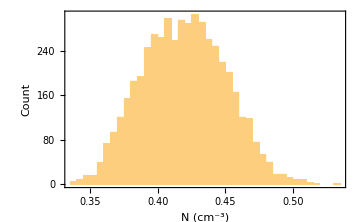
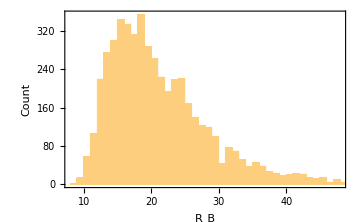
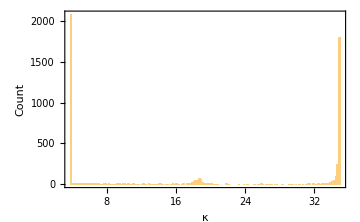
-Graphics--Graphics--Graphics--Graphics-

```mathematica
Row[Table[Histogram[kMCVals[[MCParmInd]],binSizes[[MCParmInd]],ImageSize->Medium,Frame->True,FrameLabel->{kMCTitles[[MCParmInd]],"Count"},FrameStyle->Directive[FontSize->16]],{MCParmInd,{1,2,3,4}}]]
```

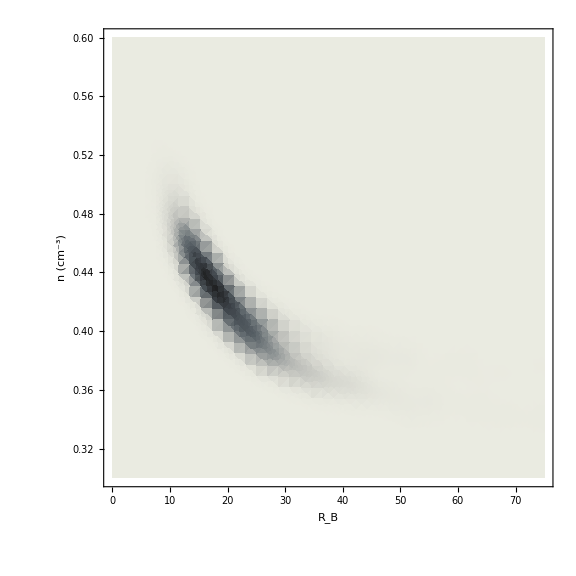

```mathematica
SmoothDensityHistogram[Partition[Riffle[kMCVals[[3]],kMCVals[[1]]],2],ImageSize->Large,PlotRange->densPlotRange,Frame->True,FrameStyle->FontSize->16, FrameLabel->{{"n (cm^-3)",""},{"R_B",Style[ToString@StringForm["`1` (Kappa, N = `2`)",MCTitle,nTrials],Bold,20]}},
ColorFunction->ColorData[{"GrayTones","Reverse"}]]
```

#### Itvl 1, fixT=124 eV, nRoll= 5000

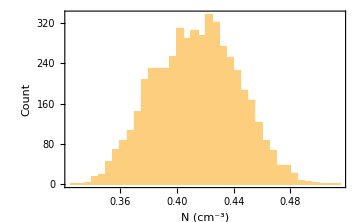
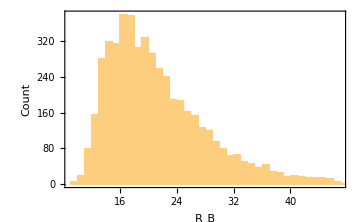
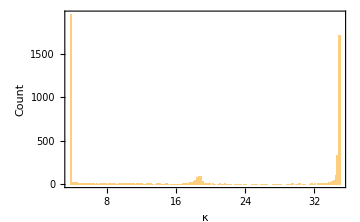
-Graphics--Graphics--Graphics--Graphics-

```mathematica
kHistosPlot=Row[Table[Histogram[kMCVals[[MCParmInd]],binSizes[[MCParmInd]],ImageSize->Medium,Frame->True,FrameLabel->{kMCTitles[[MCParmInd]],"Count"},FrameStyle->Directive[FontSize->16]],{MCParmInd,{1,2,3,4}}]]
```

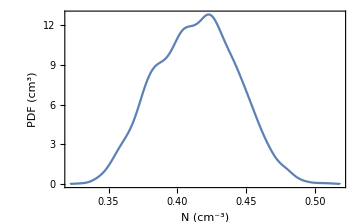
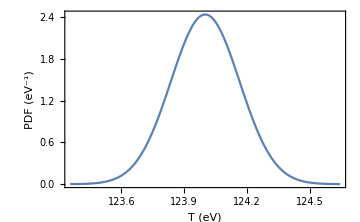
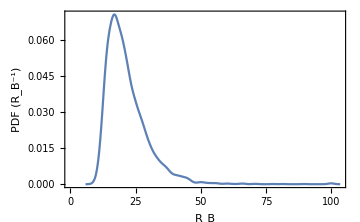
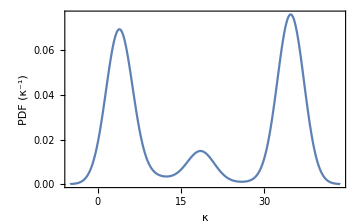

```mathematica
kSmoothHistosPlot=Row[Table[SmoothHistogram[kMCVals[[MCParmInd]],ImageSize->Medium,Frame->True,FrameLabel->{kMCTitles[[MCParmInd]],kMCPDFTitles[[MCParmInd]]},FrameStyle->Directive[FontSize->16]],{MCParmInd,{1,2,3,4}}]]
```

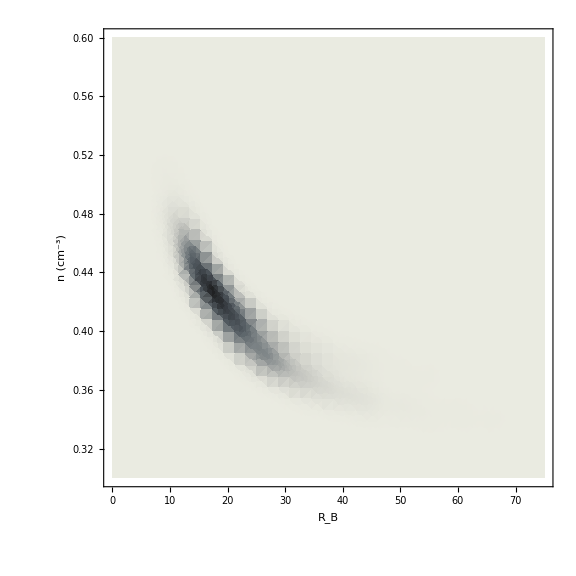

```mathematica
kDensityHisto=SmoothDensityHistogram[Partition[Riffle[kMCVals[[3]],kMCVals[[1]]],2],ImageSize->Large,PlotRange->densPlotRange,Frame->True,FrameStyle->FontSize->16, FrameLabel->{{"n (cm^-3)",""},{"R_B",Style[ToString@StringForm["`1` (Kappa, N = `2`)",MCTitle,nTrials],Bold,20]}},
ColorFunction->ColorData[{"GrayTones","Reverse"}]]
```

```mathematica
If[makePlots,Print["Making plots in "<>dir<>" ..."];
Print[kDensityHistoFile<>" ..."];
Export[plotDir<>kDensityHistoFile,kDensityHisto];
Print[kHistosPlotFile<>" ..."];
Export[plotDir<>kHistosPlotFile,kHistosPlot];
Print[kSmoothHistosPlotFile<>" ..."];
Export[plotDir<>kSmoothHistosPlotFile,kSmoothHistosPlot];
Print["Done!"]]
```

Making plots in /SPENCEdata/Research/Satellites/FAST/kappa_dists/journals/ ...

Orb1612_itvl1_kappa-fixT124eV_nRolls5000__smoothDensityHistogram.pdf ...

Orb1612_itvl1_kappa-fixT124eV_nRolls5000__histograms.pdf ...

Orb1612_itvl1_Maxwell-fixT140eV_nRolls5000__smoothHistograms.pdf ...

Done!

#### Itvl 2, fixT=193 eV, nRoll= 5000

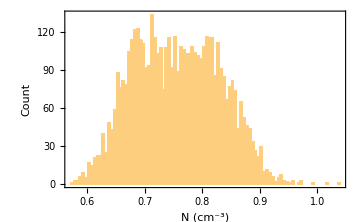
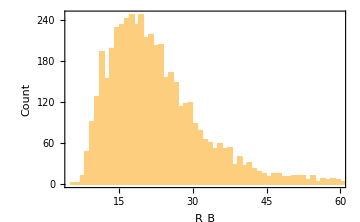
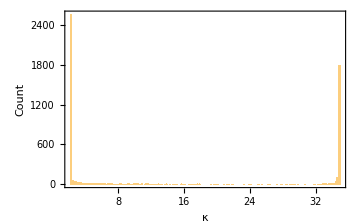
-Graphics--Graphics--Graphics--Graphics-

```mathematica
kHistosPlot=Row[Table[Histogram[kMCVals[[MCParmInd]],binSizes[[MCParmInd]],ImageSize->Medium,Frame->True,FrameLabel->{kMCTitles[[MCParmInd]],"Count"},FrameStyle->Directive[FontSize->16]],{MCParmInd,{1,2,3,4}}]]
```

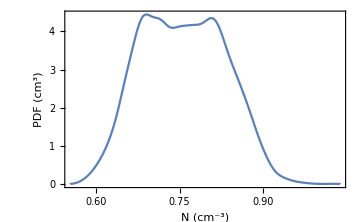
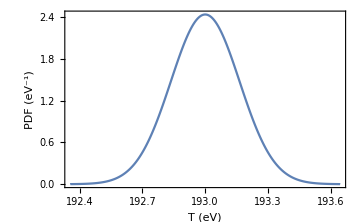
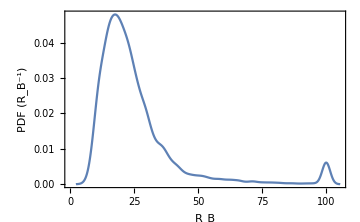
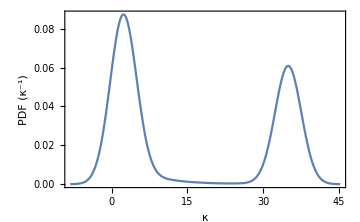

```mathematica
kSmoothHistosPlot=Row[Table[SmoothHistogram[kMCVals[[MCParmInd]],ImageSize->Medium,Frame->True,FrameLabel->{kMCTitles[[MCParmInd]],kMCPDFTitles[[MCParmInd]]},FrameStyle->Directive[FontSize->16]],{MCParmInd,{1,2,3,4}}]]
```

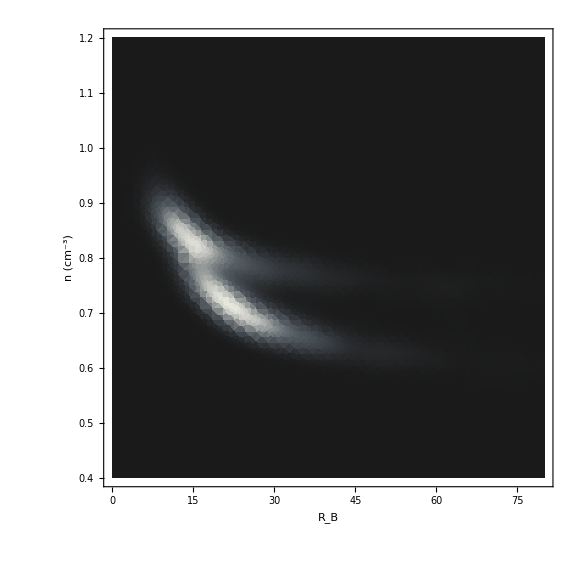

```mathematica
kDensityHisto=SmoothDensityHistogram[Partition[Riffle[kMCVals[[3]],kMCVals[[1]]],2],ImageSize->Large,PlotRange->densPlotRange,Frame->True,FrameStyle->FontSize->16, FrameLabel->{{"n (cm^-3)",""},{"R_B",Style[ToString@StringForm["`1` (Kappa, N = `2`)",MCTitle,nTrials],Bold,20]}},
ColorFunction->ColorData["GrayTones"]]
```

```mathematica
If[makePlots,Print["Making plots in "<>dir<>" ..."];
Print[kDensityHistoFile<>" ..."];
Export[plotDir<>kDensityHistoFile,kDensityHisto];
Print[kHistosPlotFile<>" ..."];
Export[plotDir<>kHistosPlotFile,kHistosPlot];
Print[kSmoothHistosPlotFile<>" ..."];
Export[plotDir<>kSmoothHistosPlotFile,kSmoothHistosPlot];
Print["Done!"]]
```

Making plots in /SPENCEdata/Research/Satellites/FAST/kappa_dists/journals/ ...

Orb1612_itvl2_kappa-fixT193eV_nRolls5000__smoothDensityHistogram.pdf ...

Orb1612_itvl2_kappa-fixT193eV_nRolls5000__histograms.pdf ...

Orb1612_itvl2_Maxwell-fixT117eV_nRolls5000__smoothHistograms.pdf ...

Done!

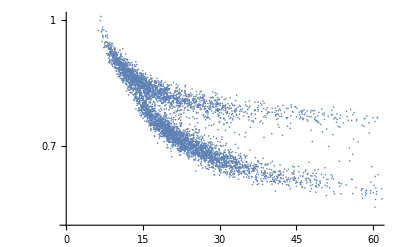

```mathematica
ListLogPlot[Partition[Riffle[kMCVals[[3]],kMCVals[[1]]],2]]
```

#### Itvl 2, fixT=193 eV, fixKappa=2.6, nRoll= 5000

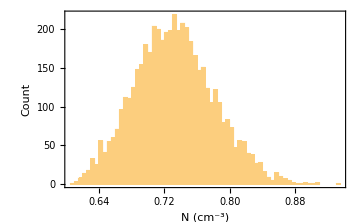
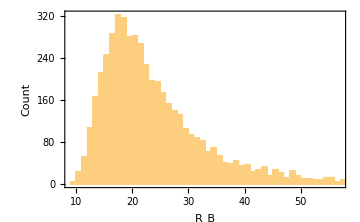
-Graphics--Graphics--Graphics--Graphics-

```mathematica
kHistosPlot=Row[Table[Histogram[kMCVals[[MCParmInd]],binSizes[[MCParmInd]],ImageSize->Medium,Frame->True,FrameLabel->{kMCTitles[[MCParmInd]],"Count"},FrameStyle->Directive[FontSize->16]],{MCParmInd,{1,2,3,4}}]]
```

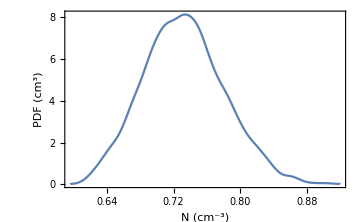
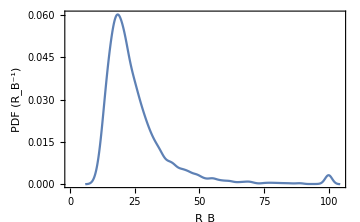
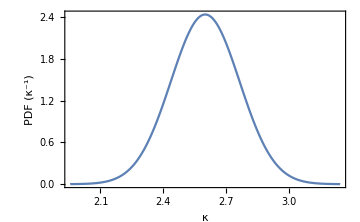
-Graphics--Graphics--Graphics--Graphics-

```mathematica
kSmoothHistosPlot=Row[Table[SmoothHistogram[kMCVals[[MCParmInd]],ImageSize->Medium,Frame->True,FrameLabel->{kMCTitles[[MCParmInd]],kMCPDFTitles[[MCParmInd]]},FrameStyle->Directive[FontSize->16]],{MCParmInd,{1,2,3,4}}]]
```

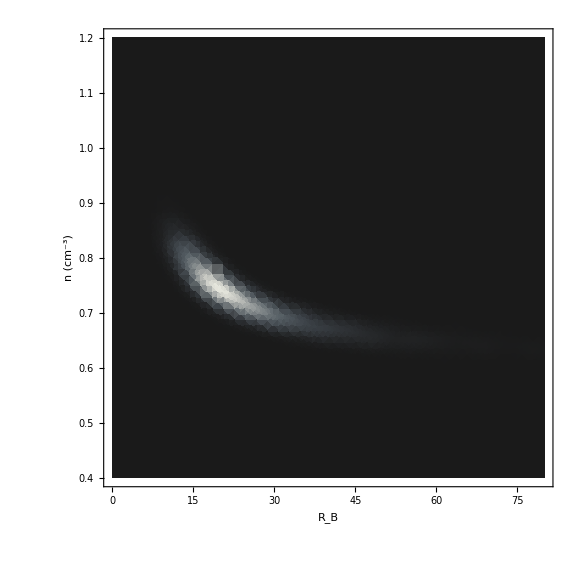

```mathematica
kDensityHisto=SmoothDensityHistogram[Partition[Riffle[kMCVals[[3]],kMCVals[[1]]],2],ImageSize->Large,PlotRange->densPlotRange,Frame->True,FrameStyle->FontSize->16, FrameLabel->{{"n (cm^-3)",""},{"R_B",Style[ToString@StringForm["`1` (Kappa, N = `2`)",MCTitle,nTrials],Bold,20]}},
ColorFunction->ColorData["GrayTones"]]
```

```mathematica
If[makePlots,Print["Making plots in "<>dir<>" ..."];
Print[kDensityHistoFile<>" ..."];
Export[plotDir<>kDensityHistoFile,kDensityHisto];
Print[kHistosPlotFile<>" ..."];
Export[plotDir<>kHistosPlotFile,kHistosPlot];
Print[kSmoothHistosPlotFile<>" ..."];
Export[plotDir<>kSmoothHistosPlotFile,kSmoothHistosPlot];
Print["Done!"]]
```

Making plots in /SPENCEdata/Research/Satellites/FAST/kappa_dists/journals/ ...

Orb1612_itvl2_kappa-fixT193eV-fixKappa2_6_nRolls5000__smoothDensityHistogram.pdf ...

Orb1612_itvl2_kappa-fixT193eV-fixKappa2_6_nRolls5000__histograms.pdf ...

Orb1612_itvl2_Maxwell-fixT117eV_nRolls5000__smoothHistograms.pdf ...

Done!

```mathematica
ListLogPlot[Partition[Riffle[kMCVals[[3]],kMCVals[[1]]],2]]
```

-Graphics-

#### Itvl 2, fixT=198 eV, nRoll= 5000

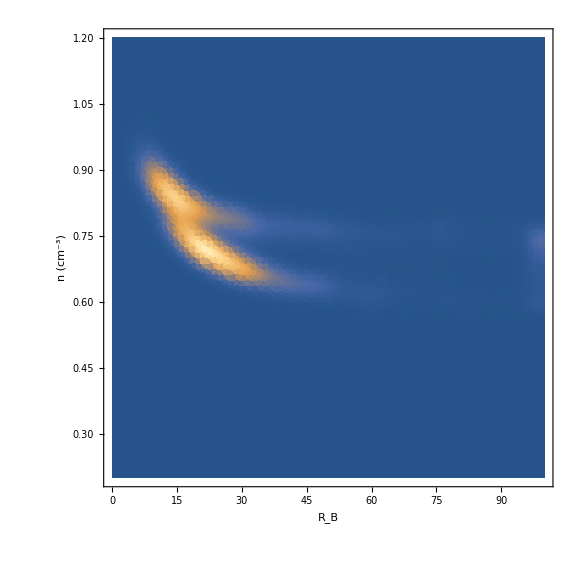

```mathematica
SmoothDensityHistogram[Partition[Riffle[kMCVals[[3]],kMCVals[[1]]],2],ImageSize->Large,PlotRange->densPlotRange,Frame->True,FrameStyle->FontSize->16, FrameLabel->{{"n (cm^-3)",""},{"R_B",Style[ToString@StringForm["`1` (Kappa, N = `2`)",MCTitle,nTrials],Bold,20]}}]
```

## Maxwellian plots

#### Itvl 1, fixT=120 eV, nRoll= 5000

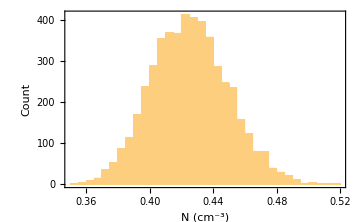
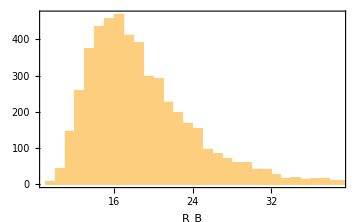
-Graphics--Graphics--Graphics-

```mathematica
Row[Table[Histogram[gMCVals[[MCParmInd]],binSizes[[MCParmInd]],ImageSize->Medium,Frame->True,FrameLabel->{gMCTitles[[MCParmInd]],If[MCParmInd==1,"Count",""]},FrameStyle->Directive[FontSize->16]],{MCParmInd,{1,2,3}}]]
```

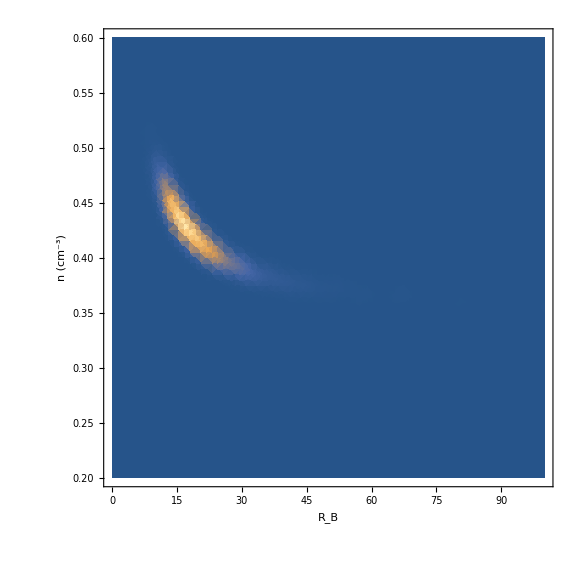

```mathematica
SmoothDensityHistogram[Partition[Riffle[gMCVals[[3]],gMCVals[[1]]],2],ImageSize->Large,PlotRange->densPlotRange,Frame->True,FrameStyle->FontSize->16, FrameLabel->{{"n (cm^-3)",""},{"R_B",Style[ToString@StringForm["`1` (Maxwellian, N = `2`)",MCTitle,nTrials],Bold,20]}}]
```

#### Itvl 1, fixT=133 eV, nRoll= 5000

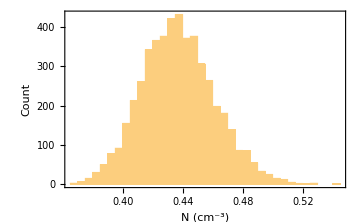
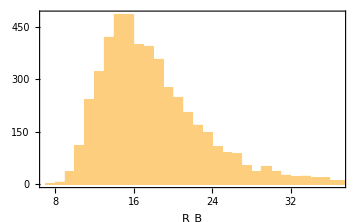
-Graphics--Graphics--Graphics-

```mathematica
Row[Table[Histogram[gMCVals[[MCParmInd]],binSizes[[MCParmInd]],ImageSize->Medium,Frame->True,FrameLabel->{gMCTitles[[MCParmInd]],If[MCParmInd==1,"Count",""]},FrameStyle->Directive[FontSize->16]],{MCParmInd,{1,2,3}}]]
```

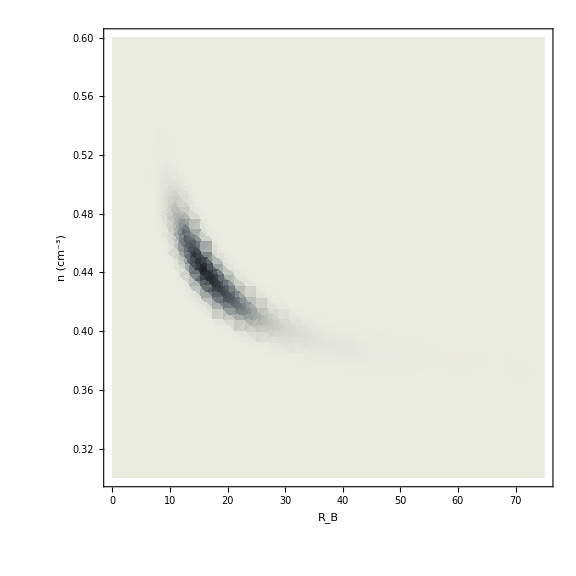

```mathematica
SmoothDensityHistogram[Partition[Riffle[gMCVals[[3]],gMCVals[[1]]],2],ImageSize->Large,PlotRange->densPlotRange,Frame->True,FrameStyle->FontSize->16, FrameLabel->{{"n (cm^-3)",""},{"R_B",Style[ToString@StringForm["`1` (Maxwellian, N = `2`)",MCTitle,nTrials],Bold,20]}},
ColorFunction->ColorData[{"GrayTones","Reverse"}]]
```

#### Itvl 1, fixT=140 eV, nRoll= 5000

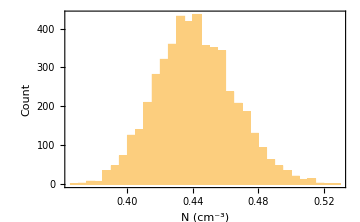
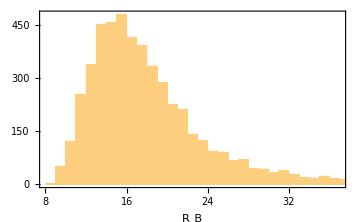
-Graphics--Graphics--Graphics-

```mathematica
gHistosPlot=Row[Table[Histogram[gMCVals[[MCParmInd]],binSizes[[MCParmInd]],ImageSize->Medium,Frame->True,FrameLabel->{gMCTitles[[MCParmInd]],If[MCParmInd==1,"Count",""]},FrameStyle->Directive[FontSize->16]],{MCParmInd,{1,2,3}}]]
```

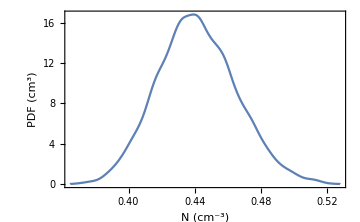
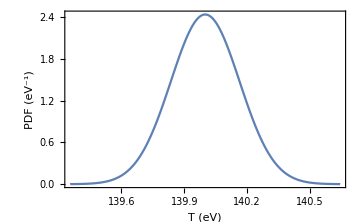
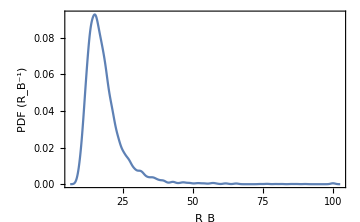

```mathematica
gSmoothHistosPlot=Row[Table[SmoothHistogram[gMCVals[[MCParmInd]],ImageSize->Medium,Frame->True,PlotRange->Full,FrameLabel->{kMCTitles[[MCParmInd]],kMCPDFTitles[[MCParmInd]]},FrameStyle->Directive[FontSize->16]],{MCParmInd,{1,2,3}}]]
```

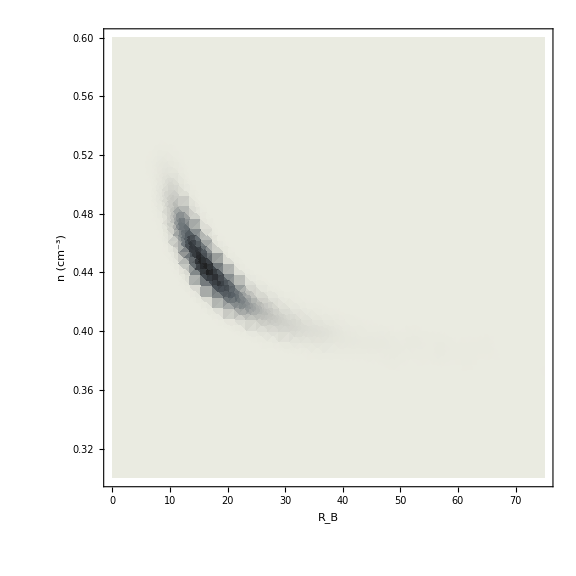

```mathematica
gDensityHisto=SmoothDensityHistogram[Partition[Riffle[gMCVals[[3]],gMCVals[[1]]],2],ImageSize->Large,PlotRange->densPlotRange,Frame->True,FrameStyle->FontSize->16, FrameLabel->{{"n (cm^-3)",""},{"R_B",Style[ToString@StringForm["`1` (Maxwellian, N = `2`)",MCTitle,nTrials],Bold,20]}},
ColorFunction->ColorData[{"GrayTones","Reverse"}]]
```

```mathematica
If[makePlots,Print["Making plots in "<>dir<>" ..."];
Print[gDensityHistoFile<>" ..."];
Export[plotDir<>gDensityHistoFile,gDensityHisto];
Print[gHistosPlotFile<>" ..."];
Export[plotDir<>gHistosPlotFile,gHistosPlot];
Print[gSmoothHistosPlotFile<>" ..."];
Export[plotDir<>gSmoothHistosPlotFile,gSmoothHistosPlot];
Print["Done!"]]
```

Making plots in /SPENCEdata/Research/Satellites/FAST/kappa_dists/journals/ ...

Orb1612_itvl1_Maxwell-fixT140eV_nRolls5000__smoothDensityHistogram.pdf ...

Orb1612_itvl1_Maxwell-fixT140eV_nRolls5000__histograms.pdf ...

Orb1612_itvl1_Maxwell-fixT140eV_nRolls5000__smoothHistograms.pdf ...

Done!

#### Itvl 2, fixT=140 eV, nRoll= 5000

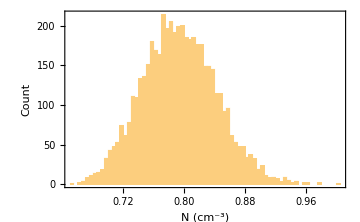
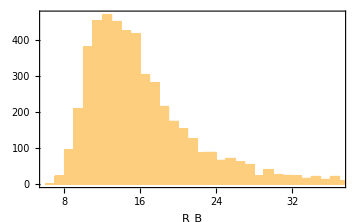
-Graphics--Graphics--Graphics-

```mathematica
Row[Table[Histogram[gMCVals[[MCParmInd]],binSizes[[MCParmInd]],ImageSize->Medium,Frame->True,FrameLabel->{gMCTitles[[MCParmInd]],If[MCParmInd==1,"Count",""]},FrameStyle->Directive[FontSize->16]],{MCParmInd,{1,2,3}}]]
```

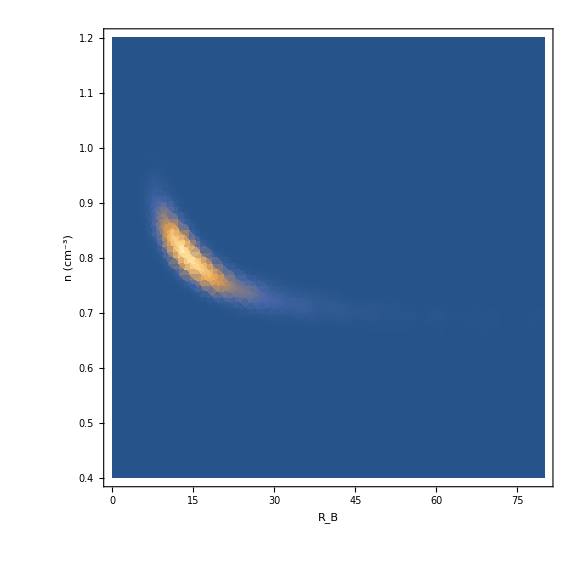

```mathematica
SmoothDensityHistogram[Partition[Riffle[gMCVals[[3]],gMCVals[[1]]],2],ImageSize->Large,PlotRange->{{0,80},{0.4,1.2}},Frame->True,FrameStyle->FontSize->16, FrameLabel->{{"n (cm^-3)",""},{"R_B",Style[ToString@StringForm["`1` (Maxwellian, N = `2`)",MCTitle,nTrials],Bold,20]}}]
```

#### Itvl 2, fixT=117 eV, nRoll= 5000

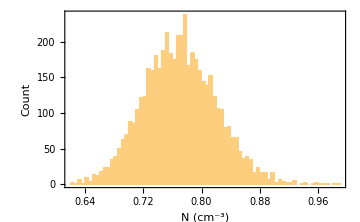
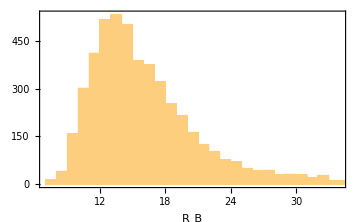
-Graphics--Graphics--Graphics-

```mathematica
gHistosPlot=Row[Table[Histogram[gMCVals[[MCParmInd]],binSizes[[MCParmInd]],ImageSize->Medium,Frame->True,FrameLabel->{gMCTitles[[MCParmInd]],If[MCParmInd==1,"Count",""]},FrameStyle->Directive[FontSize->16]],{MCParmInd,{1,2,3}}]]
```

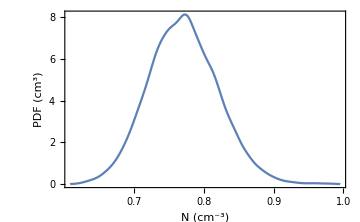
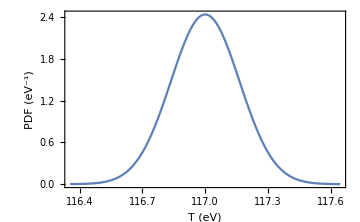
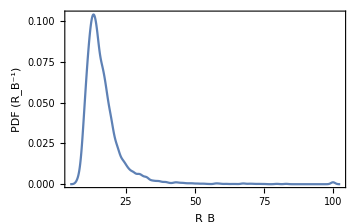

```mathematica
gSmoothHistosPlot=Row[Table[SmoothHistogram[gMCVals[[MCParmInd]],ImageSize->Medium,Frame->True,PlotRange->Full,FrameLabel->{kMCTitles[[MCParmInd]],kMCPDFTitles[[MCParmInd]]},FrameStyle->Directive[FontSize->16]],{MCParmInd,{1,2,3}}]]
```

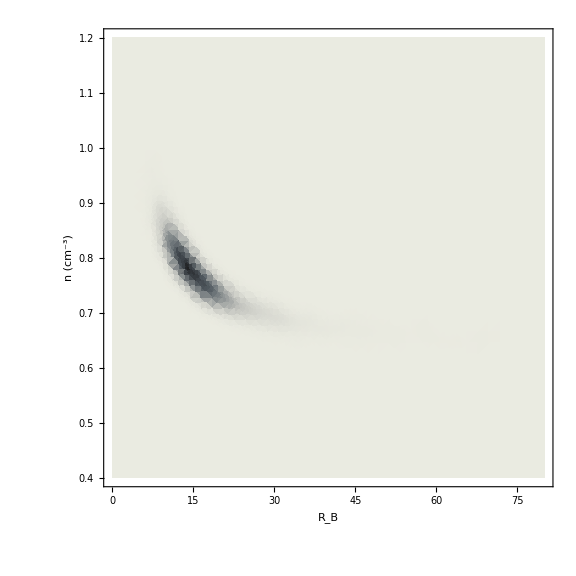

```mathematica
gDensityHisto=SmoothDensityHistogram[Partition[Riffle[gMCVals[[3]],gMCVals[[1]]],2],ImageSize->Large,PlotRange->densPlotRange,Frame->True,FrameStyle->FontSize->16, FrameLabel->{{"n (cm^-3)",""},{"R_B",Style[ToString@StringForm["`1` (Maxwellian, N = `2`)",MCTitle,nTrials],Bold,20]}},
ColorFunction->ColorData[{"GrayTones","Reverse"}]]
```

```mathematica
If[makePlots,Print["Making plots in "<>dir<>" ..."];
Print[gDensityHistoFile<>" ..."];
Export[plotDir<>gDensityHistoFile,gDensityHisto];
Print[gHistosPlotFile<>" ..."];
Export[plotDir<>gHistosPlotFile,gHistosPlot];
Print[gSmoothHistosPlotFile<>" ..."];
Export[plotDir<>gSmoothHistosPlotFile,gSmoothHistosPlot];
Print["Done!"]]
```

Making plots in /SPENCEdata/Research/Satellites/FAST/kappa_dists/journals/ ...

Orb1612_itvl2_Maxwell-fixT117eV_nRolls5000__smoothDensityHistogram.pdf ...

Orb1612_itvl2_Maxwell-fixT117eV_nRolls5000__histograms.pdf ...

Orb1612_itvl2_Maxwell-fixT117eV_nRolls5000__smoothHistograms.pdf ...

Done!

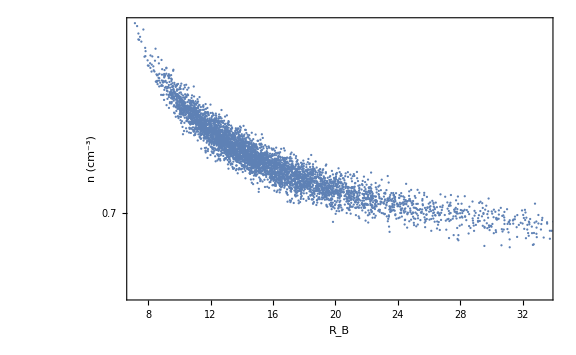

```mathematica
ListLogPlot[Partition[Riffle[gMCVals[[3]],gMCVals[[1]]],2],ImageSize->Large,Frame->True,FrameStyle->FontSize->16, FrameLabel->{{"n (cm^-3)",""},{"R_B",Style[ToString@StringForm["`1` (Maxwellian, N = `2`)",MCTitle,1000],Bold,20]}}]
```

#### Some Maxwellian/kappa combo histos

```mathematica
plotLegs=If[doFixT,
{StringForm["Maxwellian (T = `1` eV)",gfixTVal],StringForm["Kappa ∈ [`1`,`2`] (T = `3` eV)",minFitKappa,maxFitKappa,kfixTVal]},{"Maxwellian",StringForm["Kappa ∈ [`1`,`2`]",minFitKappa,maxFitKappa]}
]
```

{Maxwellian (T = 117 eV),Kappa ∈ [2.24,35] (T = 193 eV)}

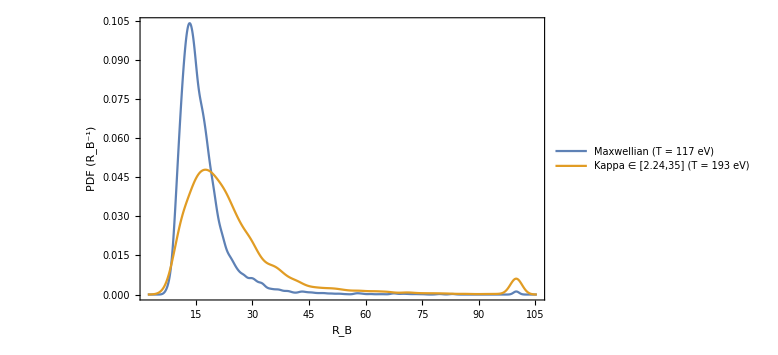

```mathematica
SmoothHistogram[{gMCVals[[3]],kMCVals[[3]]},PlotLegends->plotLegs,ImageSize->Large,PlotRange->Full,Frame->True,FrameStyle->FontSize->16, FrameLabel->{{"PDF (R_B^-1)",""},{"R_B",Style[ToString@StringForm["`1` (N = `2`)",MCTitle,nTrials],Bold,20]}}]
```

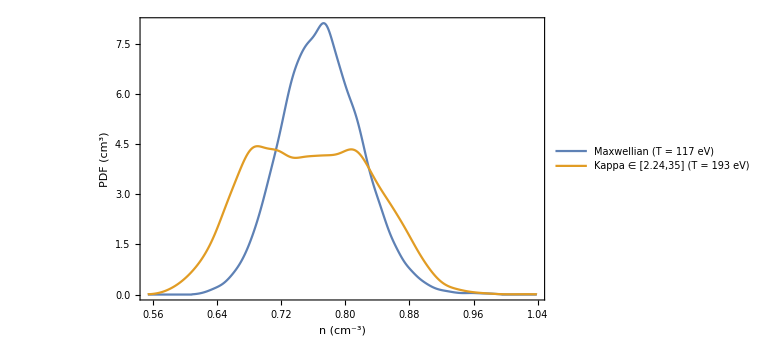

```mathematica
SmoothHistogram[{gMCVals[[1]],kMCVals[[1]]},PlotLegends->plotLegs,ImageSize->Large,PlotRange->Full,Frame->True,FrameStyle->FontSize->16, FrameLabel->{{"PDF (cm^3)",""},{"n (cm^-3)",Style[ToString@StringForm["`1` (N = `2`)",MCTitle,nTrials],Bold,20]}}]
```